# RQA Exploration

Alison Ord

Flip Phillips

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

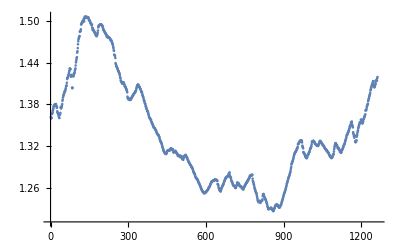

```mathematica
ListPlot[data]
```

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

```mathematica
RQAEstimateDimensionality[ds,lag]
```

Part::partw: Part 1212 of {{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},{1.37293,1.3915},«32»,{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},«906»} does not exist.

MapThread::mptd: Object {{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},{1.37293,1.3915},«32»,{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},«906»}⟦{1212,383,«47»,356,«1212»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},«33»,{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},«906»},{«1»,«50»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

MapThread[SquaredEuclideanDistance,{{{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},{1.37293,1.3915},{1.37495,1.3919},{1.3773,1.39302},{1.37773,1.39365},{1.37799,1.39411},{1.3791,1.39457},{1.37932,1.39513},{1.38022,1.3961},{1.37992,1.39667},{1.38041,1.39665},{1.38033,1.39673},{1.38052,1.39764},{1.37801,1.39884},{1.37779,1.39924},{1.37514,1.39991},{1.37596,1.40177},{1.37021,1.4033},{1.3682,1.40467},{1.36809,1.40635},{1.36756,1.40687},{1.36544,1.40737},{1.36541,1.40819},{1.36268,1.40859},{1.36138,1.40828},{1.36046,1.40634},{1.36508,1.40614},{1.36545,1.40596},{1.36611,1.40553},{1.3679,1.4047},{1.37607,1.40388},{1.37455,1.40272},{1.37444,1.40233},{1.37602,1.40149},{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},{1.39437,1.39141},{1.39544,1.3907},{1.39648,1.38922},{1.39828,1.38676},{1.39844,1.38601},{1.39916,1.38555},{1.40001,1.3836},{1.40192,1.38243},{1.40334,1.38126},{1.40611,1.38056},{1.40649,1.37859},{1.40746,1.37707},{1.41115,1.37661},{1.41644,1.37505},{1.41821,1.37362},{1.41801,1.37325},{1.4191,1.37131},{1.42136,1.37047},{1.42209,1.37019},{1.4231,1.36947},{1.42533,1.36816},{1.42718,1.36642},{1.42859,1.36506},{1.43141,1.36323},{1.43147,1.36184},{1.43087,1.36114},{1.43049,1.36036},{1.42014,1.35984},{1.42004,1.35944},{1.42255,1.3586},{1.42093,1.35807},{1.4211,1.35789},{1.40406,1.35629},{1.40315,1.35515},{1.40407,1.35368},{1.42051,1.35296},{1.42136,1.35267},{1.42045,1.35143},{1.42077,1.35075},{1.42398,1.34951},{1.42422,1.34896},{1.42453,1.34763},{1.42622,1.34687},{1.4285,1.34648},{1.43024,1.34625},{1.43176,1.34606},{1.43594,1.34577},{1.44023,1.34458},{1.44224,1.34372},{1.44459,1.34344},{1.44675,1.34298},{1.44773,1.34196},{1.45431,1.34069},{1.45642,1.3397},{1.46088,1.33895},{1.46635,1.33796},{1.47059,1.33751},{1.47342,1.33686},{1.475,1.33655},{1.47642,1.33629},{1.47692,1.33574},{1.47833,1.33509},{1.48425,1.3342},{1.48467,1.33351},{1.48501,1.33185},{1.48544,1.3301},{1.48783,1.32896},{1.49456,1.32794},{1.4955,1.32703},{1.49586,1.32647},{1.49741,1.32581},{1.49793,1.32449},{1.49925,1.32391},{1.4988,1.32292},{1.49783,1.32122},{1.49914,1.31947},{1.50087,1.31839},{1.50201,1.31704},{1.50305,1.31597},{1.49928,1.31456},{1.50431,1.31329},{1.50508,1.31274},{1.50585,1.31215},{1.50622,1.3111},{1.50455,1.31076},{1.50396,1.31028},{1.50439,1.30983},{1.50487,1.3095},{1.50546,1.30926},{1.5058,1.30888},{1.50466,1.30932},{1.50476,1.31012},{1.50419,1.31115},{1.50504,1.3123},{1.50446,1.31314},{1.5049,1.31369},{1.50349,1.31391},{1.50148,1.31402},{1.50148,1.31406},{1.50045,1.31442},{1.49964,1.31448},{1.49957,1.31402},{1.49866,1.31359},{1.49675,1.31427},{1.49606,1.315},{1.49579,1.31553},{1.49605,1.31601},{1.49477,1.31651},{1.49322,1.31687},{1.49416,1.31708},{1.49016,1.31556},{1.48728,1.31497},{1.48847,1.31479},{1.48906,1.31554},{1.48706,1.31577},{1.48572,1.31558},{1.48608,1.31501},{1.48467,1.31254},{1.48462,1.31157},{1.48354,1.31124},{1.48207,1.31146},{1.48256,1.31194},{1.48229,1.31207},{1.48006,1.3127},{1.47943,1.31317},{1.47883,1.31331},{1.47855,1.31303},{1.47779,1.31176},{1.47855,1.31123},{1.48019,1.31102},{1.48106,1.3101},{1.48334,1.30977},{1.48607,1.30966},{1.49052,1.30872},{1.4915,1.30724},{1.49298,1.30633},{1.49327,1.3062},{1.49364,1.30618},{1.4939,1.30679},{1.49413,1.30681},{1.49433,1.30669},{1.49472,1.30699},{1.49444,1.30672},{1.49472,1.30492},{1.49478,1.30481},{1.49403,1.30549},{1.4945,1.3053},{1.4937,1.30526},{1.49242,1.30517},{1.49262,1.30559},{1.49267,1.30356},{1.49022,1.30274},{1.48911,1.30192},{1.48727,1.30153},{1.48698,1.30142},{1.48585,1.30078},{1.48546,1.30206},{1.48471,1.30355},{1.48396,1.30442},{1.48363,1.30518},{1.48286,1.30558},{1.48231,1.30636},{1.48096,1.30678},{1.48092,1.30694},{1.48003,1.30718},{1.47967,1.30749},{1.47751,1.30631},{1.47685,1.30551},{1.4786,1.3052},{1.47733,1.304},{1.47603,1.3035},{1.47652,1.30315},{1.47664,1.30177},{1.47567,1.30074},{1.47578,1.29995},{1.4755,1.29889},{1.4754,1.298},{1.47553,1.29722},{1.47498,1.29685},{1.47385,1.29624},{1.47312,1.29537},{1.4727,1.29436},{1.47173,1.29389},{1.4725,1.2932},{1.47082,1.29273},{1.4707,1.29247},{1.46956,1.29197},{1.46826,1.29082},{1.46712,1.28982},{1.46615,1.28933},{1.4643,1.28903},{1.46213,1.28824},{1.46072,1.28755},{1.45779,1.286},{1.45677,1.28461},{1.4514,1.28362},{1.45091,1.28247},{1.45036,1.28186},{1.44944,1.28132},{1.44661,1.28077},{1.4393,1.27983},{1.43774,1.27887},{1.43676,1.2772},{1.4347,1.27592},{1.43432,1.27527},{1.43393,1.27474},{1.43215,1.27428},{1.43182,1.27389},{1.431,1.27335},{1.42921,1.27257},{1.42776,1.27256},{1.42809,1.27184},{1.42765,1.27087},{1.42581,1.26995},{1.42523,1.26876},{1.42425,1.26781},{1.42282,1.26747},{1.42057,1.26672},{1.41813,1.26549},{1.41759,1.26478},{1.41453,1.26414},{1.41339,1.26309},{1.41301,1.26205},{1.41232,1.26116},{1.41136,1.26033},{1.41033,1.25919},{1.40984,1.25819},{1.41059,1.25758},{1.41078,1.25685},{1.41191,1.25604},{1.41159,1.25519},{1.41124,1.25488},{1.41019,1.25449},{1.40918,1.25407},{1.40851,1.25366},{1.40673,1.25335},{1.40586,1.25276},{1.40553,1.25249},{1.40549,1.25357},{1.40407,1.25387},{1.40325,1.25368},{1.40223,1.2537},{1.40169,1.25381},{1.40017,1.25404},{1.39935,1.25443},{1.39729,1.25536},{1.39116,1.25579},{1.38904,1.25614},{1.3889,1.25661},{1.389,1.2569},{1.3871,1.25728},{1.38836,1.25786},{1.38832,1.2584},{1.38789,1.25994},{1.38675,1.2606},{1.38663,1.26088},{1.38632,1.26132},{1.38687,1.26226},{1.38714,1.26286},{1.38731,1.2637},{1.38795,1.26475},{1.38904,1.26583},{1.38974,1.26689},{1.39041,1.26719},{1.39095,1.26817},{1.39171,1.26897},{1.39198,1.2696},{1.39341,1.26975},{1.39374,1.26986},{1.39426,1.27049},{1.3947,1.27036},{1.3953,1.27028},{1.3964,1.27052},{1.39677,1.27076},{1.39661,1.27074},{1.39677,1.27135},{1.39797,1.27155},{1.39917,1.27213},{1.39927,1.27219},{1.40015,1.2719},{1.40238,1.27162},{1.40365,1.27173},{1.40506,1.27181},{1.40683,1.27174},{1.40689,1.27171},{1.40755,1.27104},{1.40843,1.27111},{1.40866,1.2704},{1.40814,1.26702},{1.40566,1.26552},{1.40632,1.26484},{1.40583,1.2636},{1.40542,1.26133},{1.40442,1.25991},{1.40367,1.2591},{1.40237,1.25822},{1.40231,1.25694},{1.40118,1.2564},{1.40005,1.25584},{1.39826,1.25596},{1.39754,1.25537},{1.39846,1.25693},{1.39752,1.25859},{1.39533,1.25948},{1.39307,1.26031},{1.39274,1.26152},{1.39091,1.26223},{1.39062,1.26302},{1.38869,1.26386},{1.38603,1.26468},{1.38601,1.26501},{1.38538,1.26588},{1.38294,1.26734},{1.38224,1.26873},{1.38089,1.26967},{1.38043,1.2704},{1.3779,1.27159},{1.37676,1.27271},{1.37655,1.27307},{1.37449,1.27424},{1.3733,1.27471},{1.37323,1.27552},{1.37059,1.27566},{1.37042,1.27577},{1.3701,1.27626},{1.36924,1.27603},{1.36776,1.27625},{1.36592,1.27693},{1.36473,1.2773},{1.36267,1.27788},{1.36153,1.27913},{1.36099,1.27989},{1.36013,1.27999},{1.35974,1.28123},{1.35932,1.28226},{1.35832,1.27949},{1.35797,1.27745},{1.35786,1.27621},{1.3557,1.27559},{1.35494,1.27489},{1.35321,1.27357},{1.35287,1.2715},{1.35259,1.27013},{1.35099,1.26922},{1.35066,1.26895},{1.34908,1.26791},{1.34891,1.26665},{1.34714,1.26542},{1.34677,1.26456},{1.34637,1.2639},{1.34621,1.26345},{1.346,1.26343},{1.34568,1.26284},{1.34416,1.26263},{1.34356,1.26261},{1.3434,1.26247},{1.34282,1.26098},{1.34164,1.26016},{1.34034,1.26028},{1.33946,1.26077},{1.33875,1.26225},{1.33766,1.2634},{1.33745,1.2644},{1.33664,1.26691},{1.33652,1.26778},{1.33621,1.26724},{1.33556,1.26723},{1.33492,1.26735},{1.33393,1.26649},{1.33336,1.26641},{1.33128,1.26626},{1.32966,1.26539},{1.32869,1.26412},{1.32766,1.26355},{1.32679,1.26336},{1.32634,1.26278},{1.3256,1.26225},{1.32407,1.26217},{1.32385,1.26199},{1.32257,1.26186},{1.32071,1.2618},{1.319,1.26074},{1.31817,1.25994},{1.31661,1.25968},{1.31573,1.25956},{1.31412,1.25942},{1.31298,1.25938},{1.31264,1.25817},{1.31196,1.25901},{1.31077,1.26048},{1.31076,1.26129},{1.3101,1.26149},{1.30973,1.26225},{1.30941,1.26345},{1.3092,1.26441},{1.30876,1.26457},{1.30953,1.26506},{1.31034,1.26628},{1.31145,1.26663},{1.31262,1.26748},{1.31334,1.26789},{1.31383,1.26819},{1.31395,1.26841},{1.31405,1.26992},{1.31406,1.2706},{1.31456,1.27084},{1.31445,1.27108},{1.31386,1.27229},{1.31349,1.27318},{1.31456,1.27383},{1.31517,1.27456},{1.31566,1.27516},{1.31615,1.2763},{1.31664,1.27758},{1.31695,1.27758},{1.31713,1.2778},{1.31497,1.27766},{1.31498,1.27831},{1.31472,1.2782},{1.31585,1.27856},{1.31574,1.27875},{1.31552,1.27918},{1.31481,1.27869},{1.31168,1.27486},{1.31152,1.27118},{1.31114,1.26948},{1.31158,1.26842},{1.31208,1.2666},{1.31207,1.26532},{1.31293,1.26403},{1.31326,1.26191},{1.31333,1.26007},{1.31292,1.2586},{1.31132,1.25794},{1.31119,1.25629},{1.31096,1.2552},{1.30977,1.25395},{1.30977,1.25331},{1.30962,1.25235},{1.30838,1.25065},{1.30681,1.24866},{1.30616,1.24686},{1.30622,1.2447},{1.30617,1.24264},{1.30703,1.24159},{1.30673,1.24097},{1.30668,1.24009},{1.30711,1.24003},{1.30657,1.24113},{1.3043,1.24164},{1.30501,1.24102},{1.30567,1.24055},{1.30516,1.23997},{1.30529,1.239},{1.30513,1.23963},{1.30576,1.24076},{1.30273,1.2415},{1.30274,1.24155},{1.30161,1.2415},{1.3015,1.24178},{1.30139,1.24197},{1.30056,1.2433},{1.30262,1.24713},{1.3039,1.25023},{1.30461,1.25096},{1.30539,1.25143},{1.30565,1.25107},{1.30663,1.24979},{1.30684,1.2481},{1.30698,1.24683},{1.30725,1.24606},{1.30758,1.24505},{1.30583,1.2447},{1.30539,1.24398},{1.30513,1.24281},{1.30357,1.24231},{1.30347,1.24075},{1.30303,1.23962},{1.30129,1.23824},{1.30054,1.23717},{1.29972,1.23481},{1.29858,1.23377},{1.29779,1.23264},{1.29701,1.23113},{1.29679,1.2298},{1.29604,1.22996},{1.29512,1.2302},{1.29407,1.23022},{1.29382,1.23023},{1.29297,1.23046},{1.29265,1.23059},{1.29241,1.2308},{1.29181,1.23099},{1.29045,1.23123},{1.28959,1.23168},{1.28923,1.23174},{1.28896,1.23052},{1.28797,1.23009},{1.28739,1.23004},{1.28548,1.2294},{1.28429,1.22897},{1.28337,1.22827},{1.28213,1.22741},{1.28175,1.22705},{1.28116,1.22736},{1.28062,1.22845},{1.27953,1.22976},{1.27862,1.23055},{1.27667,1.23115},{1.27563,1.23263},{1.27513,1.23376},{1.27459,1.23431},{1.27417,1.23505},{1.27378,1.23564},{1.27319,1.23617},{1.27234,1.23626},{1.27265,1.23572},{1.27154,1.23561},{1.27061,1.23577},{1.2697,1.23602},{1.2684,1.23555},{1.26759,1.23501},{1.26742,1.23431},{1.26645,1.23341},{1.26513,1.233},{1.26464,1.23244},{1.26395,1.23212},{1.26277,1.23205},{1.26179,1.23265},{1.26092,1.2333},{1.2601,1.23396},{1.25884,1.23498},{1.25794,1.23553},{1.25745,1.23601},{1.25663,1.23714},{1.25582,1.23882},{1.25496,1.2403},{1.25485,1.24111},{1.25435,1.24234},{1.25397,1.24369},{1.25354,1.24531},{1.25327,1.24645},{1.25257,1.24806},{1.25246,1.24958},{1.25399,1.25107},{1.25383,1.25197},{1.25363,1.253},{1.25373,1.25388},{1.25385,1.25504},{1.25411,1.25626},{1.25456,1.25734},{1.25566,1.25896},{1.25585,1.26021},{1.25626,1.26183},{1.25675,1.2634},{1.25695,1.26546},{1.2574,1.26684},{1.25804,1.26806},{1.25853,1.26929},{1.26048,1.27072},{1.26065,1.27198},{1.26096,1.27383},{1.26146,1.27485},{1.26256,1.27591},{1.26298,1.27668},{1.26397,1.27788},{1.26505,1.27909},{1.26613,1.28054},{1.26717,1.28188},{1.26719,1.28305},{1.26854,1.2851},{1.26914,1.28773},{1.26978,1.28988},{1.26974,1.29286},{1.26991,1.29497},{1.27071,1.29572},{1.27023,1.29684},{1.27029,1.29807},{1.27061,1.29887},{1.27082,1.30004},{1.27071,1.30164},{1.27159,1.303},{1.27153,1.30499},{1.27235,1.30662},{1.27213,1.30783},{1.27182,1.30923},{1.27154,1.31008},{1.27181,1.31102},{1.27181,1.31145},{1.27171,1.31198},{1.27171,1.31278},{1.27078,1.31309},{1.27123,1.31391},{1.27009,1.31496},{1.26586,1.31603},{1.26539,1.31689},{1.26463,1.31722},{1.26321,1.31876},{1.26061,1.32196},{1.25964,1.32316},{1.2589,1.32378},{1.25796,1.32407},{1.25655,1.32443},{1.25634,1.32573},{1.25565,1.32613},{1.25608,1.32688},{1.2551,1.32719},{1.25762,1.32732},{1.25895,1.32812},{1.25969,1.32853},{1.26055,1.32779},{1.26189,1.32752},{1.26235,1.32806},{1.26328,1.32794},{1.26407,1.32607},{1.26491,1.32215},{1.26505,1.31991},{1.26619,1.31869},{1.26777,1.3174},{1.2691,1.31317},{1.26989,1.31133},{1.2706,1.31039},{1.27197,1.30947},{1.27298,1.30951},{1.2731,1.30894},{1.27467,1.30743},{1.27472,1.30593},{1.27582,1.30574},{1.2756,1.3046},{1.27583,1.30435},{1.27643,1.3046},{1.27589,1.30329},{1.27638,1.30356},{1.27714,1.30345},{1.27736,1.30442},{1.27807,1.30627},{1.27953,1.30724},{1.28002,1.30784},{1.27998,1.30813},{1.2817,1.30908},{1.28247,1.31006},{1.27836,1.31105},{1.27711,1.3117},{1.27587,1.31219},{1.27548,1.31397},{1.27467,1.31575},{1.27316,1.31637},{1.27087,1.31704},{1.26985,1.31781},{1.26898,1.31866},{1.26894,1.32},{1.26752,1.32228},{1.26632,1.32519},{1.26508,1.32658},{1.26436,1.32687},{1.26373,1.32709},{1.26334,1.32721},{1.26347,1.32739},{1.2626,1.32784},{1.26265,1.32728},{1.2626,1.32698},{1.26242,1.32672},{1.26044,1.32592},{1.26006,1.32451},{1.26037,1.32373},{1.26092,1.32368},{1.26276,1.32345},{1.26365,1.32284},{1.26469,1.32219},{1.26774,1.32168},{1.26779,1.32162},{1.26704,1.32173},{1.26731,1.32105},{1.26736,1.32079},{1.26616,1.32135},{1.26651,1.3216},{1.26617,1.32067},{1.2651,1.32122},{1.26375,1.32252},{1.26348,1.32328},{1.26331,1.32361},{1.26259,1.32535},{1.26213,1.32642},{1.26219,1.32744},{1.26191,1.32758},{1.26184,1.32713},{1.26179,1.32679},{1.26035,1.32595},{1.25978,1.32566},{1.25964,1.32516},{1.25954,1.32455},{1.25938,1.32406},{1.25939,1.32296},{1.25771,1.32263},{1.2595,1.3222},{1.26084,1.3216},{1.26145,1.32128},{1.2615,1.32075},{1.26254,1.32032},{1.26379,1.31926},{1.26465,1.31844},{1.26454,1.31822},{1.26526,1.31751},{1.26666,1.31676},{1.26662,1.31623},{1.2678,1.31594},{1.26793,1.31536},{1.26829,1.31433},{1.26845,1.31426},{1.27047,1.31455},{1.27065,1.31405},{1.27091,1.313},{1.27114,1.31223},{1.27272,1.3122},{1.27336,1.31156},{1.274,1.31113},{1.27478,1.31045},{1.27531,1.30989},{1.27668,1.30863},{1.27793,1.30785},{1.27744,1.30776},{1.27794,1.30636},{1.27756,1.30569},{1.2786,1.30529},{1.27805,1.305},{1.27876,1.30427},{1.27874,1.30356},{1.27934,1.30322},{1.27844,1.30328},{1.27351,1.30333},{1.27031,1.30384},{1.26917,1.30436},{1.26814,1.30579},{1.26603,1.30703},{1.26505,1.3077},{1.26364,1.30815},{1.26126,1.30934},{1.25963,1.31187},{1.25822,1.31512},{1.25783,1.31778},{1.25571,1.31966},{1.25502,1.32146},{1.25355,1.32311},{1.25322,1.32398},{1.25203,1.32446},{1.25012,1.32338},{1.24811,1.32239},{1.24639,1.32204},{1.24407,1.32195},{1.24211,1.32167},{1.2414,1.32027},{1.24081,1.31895},{1.23982,1.31738},{1.2401,1.31726},{1.24152,1.3174},{1.24168,1.3175},{1.24078,1.31707},{1.24046,1.31579},{1.23979,1.31499},{1.23871,1.3144},{1.23997,1.31301},{1.24105,1.31225},{1.24166,1.31158},{1.2415,1.31137},{1.2415,1.31121},{1.24188,1.31077},{1.242,1.31158},{1.24379,1.31316},{1.24839,1.31417},{1.25092,1.31502},{1.25097,1.31561},{1.25161,1.31658},{1.25087,1.31771},{1.24939,1.31843},{1.24761,1.31999},{1.24653,1.32081},{1.24588,1.32165},{1.24474,1.32245},{1.24469,1.32336},{1.24371,1.32438},{1.24247,1.32584},{1.24225,1.32747},{1.24019,1.32868},{1.23941,1.32968},{1.2378,1.33124},{1.23694,1.33271},{1.23401,1.33485},{1.23368,1.33604},{1.23225,1.33644},{1.23071,1.33679},{1.22946,1.33858},{1.23015,1.33943},{1.23022,1.3397},{1.23023,1.34091},{1.23023,1.34204},{1.23055,1.34294},{1.23061,1.34468},{1.23088,1.34568},{1.23103,1.3477},{1.23131,1.34817},{1.23182,1.34867},{1.23171,1.35011},{1.23008,1.35121},{1.23009,1.35329},{1.23003,1.35428},{1.22917,1.35384},{1.2289,1.35502},{1.22803,1.35251},{1.22717,1.34999},{1.22701,1.3489},{1.2275,1.34751},{1.22881,1.34206},{1.23011,1.33892},{1.23071,1.33731},{1.23131,1.33538},{1.23312,1.33419},{1.234,1.3327},{1.23442,1.33435},{1.23529,1.33512},{1.23578,1.32948},{1.23632,1.32621},{1.23624,1.32617},{1.23552,1.32628},{1.23565,1.32752},{1.23582,1.32835},{1.2361,1.33227},{1.23534,1.33509},{1.23489,1.33695},{1.23409,1.33942},{1.23316,1.34123},{1.23294,1.34265},{1.23225,1.34522},{1.23208,1.3469},{1.23204,1.3484},{1.23289,1.3496},{1.23346,1.35112},{1.23415,1.35224},{1.2353,1.35385},{1.23561,1.35416},{1.23616,1.35429},{1.23751,1.35449},{1.23931,1.35701},{1.24068,1.35803},{1.24127,1.35786},{1.24275,1.35665},{1.24405,1.35468},{1.24578,1.35351},{1.24671,1.35294},{1.24856,1.35331},{1.24996,1.35434},{1.25149,1.35561},{1.25215,1.35789},{1.25332,1.35913},{1.25409,1.36008},{1.25541,1.36119},{1.25659,1.36217},{1.25762,1.36342},{1.25946,1.36464},{1.26049,1.36553},{1.26234,1.36976},{1.26381,1.37151},{1.26609,1.37203},{1.26713,1.37204},{1.26842,1.37372},{1.26962,1.37611},{1.27113,1.37787},{1.2723,1.37876},{1.27441,1.3798},{1.27501,1.38072},{1.27625,1.38363},{1.27685,1.38598},{1.27827,1.38712},{1.27939,1.3887},{1.28097,1.39047},{1.28223,1.39189},{1.28337,1.39352},{1.28575,1.39455},{1.28847,1.39633},{1.29041,1.39941},{1.29378,1.4009},{1.29542,1.40256},{1.29584,1.40383},{1.29722,1.40516},{1.29839,1.40647},{1.29905,1.40777},{1.30042,1.40891},{1.3021,1.40976},{1.30334,1.41107},{1.30562,1.41283},{1.307,1.41326},{1.30814,1.41291},{1.30964,1.40913},{1.31024,1.40611},{1.31132,1.40477},{1.3115,1.40493},{1.31216,1.40612},{1.31301,1.40746},{1.31312,1.40866},{1.31421,1.41012},{1.31525,1.41346},{1.31633,1.41409},{1.31711,1.4142},{1.31726,1.41415},{1.31933,1.41425},{1.32295,1.41659},{1.32324,1.41883}},{{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},{1.37293,1.3915},{1.37495,1.3919},{1.3773,1.39302},{1.37773,1.39365},{1.37799,1.39411},{1.3791,1.39457},{1.37932,1.39513},{1.38022,1.3961},{1.37992,1.39667},{1.38041,1.39665},{1.38033,1.39673},{1.38052,1.39764},{1.37801,1.39884},{1.37779,1.39924},{1.37514,1.39991},{1.37596,1.40177},{1.37021,1.4033},{1.3682,1.40467},{1.36809,1.40635},{1.36756,1.40687},{1.36544,1.40737},{1.36541,1.40819},{1.36268,1.40859},{1.36138,1.40828},{1.36046,1.40634},{1.36508,1.40614},{1.36545,1.40596},{1.36611,1.40553},{1.3679,1.4047},{1.37607,1.40388},{1.37455,1.40272},{1.37444,1.40233},{1.37602,1.40149},{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},{1.39437,1.39141},{1.39544,1.3907},{1.39648,1.38922},{1.39828,1.38676},{1.39844,1.38601},{1.39916,1.38555},{1.40001,1.3836},{1.40192,1.38243},{1.40334,1.38126},{1.40611,1.38056},{1.40649,1.37859},{1.40746,1.37707},{1.41115,1.37661},{1.41644,1.37505},{1.41821,1.37362},{1.41801,1.37325},{1.4191,1.37131},{1.42136,1.37047},{1.42209,1.37019},{1.4231,1.36947},{1.42533,1.36816},{1.42718,1.36642},{1.42859,1.36506},{1.43141,1.36323},{1.43147,1.36184},{1.43087,1.36114},{1.43049,1.36036},{1.42014,1.35984},{1.42004,1.35944},{1.42255,1.3586},{1.42093,1.35807},{1.4211,1.35789},{1.40406,1.35629},{1.40315,1.35515},{1.40407,1.35368},{1.42051,1.35296},{1.42136,1.35267},{1.42045,1.35143},{1.42077,1.35075},{1.42398,1.34951},{1.42422,1.34896},{1.42453,1.34763},{1.42622,1.34687},{1.4285,1.34648},{1.43024,1.34625},{1.43176,1.34606},{1.43594,1.34577},{1.44023,1.34458},{1.44224,1.34372},{1.44459,1.34344},{1.44675,1.34298},{1.44773,1.34196},{1.45431,1.34069},{1.45642,1.3397},{1.46088,1.33895},{1.46635,1.33796},{1.47059,1.33751},{1.47342,1.33686},{1.475,1.33655},{1.47642,1.33629},{1.47692,1.33574},{1.47833,1.33509},{1.48425,1.3342},{1.48467,1.33351},{1.48501,1.33185},{1.48544,1.3301},{1.48783,1.32896},{1.49456,1.32794},{1.4955,1.32703},{1.49586,1.32647},{1.49741,1.32581},{1.49793,1.32449},{1.49925,1.32391},{1.4988,1.32292},{1.49783,1.32122},{1.49914,1.31947},{1.50087,1.31839},{1.50201,1.31704},{1.50305,1.31597},{1.49928,1.31456},{1.50431,1.31329},{1.50508,1.31274},{1.50585,1.31215},{1.50622,1.3111},{1.50455,1.31076},{1.50396,1.31028},{1.50439,1.30983},{1.50487,1.3095},{1.50546,1.30926},{1.5058,1.30888},{1.50466,1.30932},{1.50476,1.31012},{1.50419,1.31115},{1.50504,1.3123},{1.50446,1.31314},{1.5049,1.31369},{1.50349,1.31391},{1.50148,1.31402},{1.50148,1.31406},{1.50045,1.31442},{1.49964,1.31448},{1.49957,1.31402},{1.49866,1.31359},{1.49675,1.31427},{1.49606,1.315},{1.49579,1.31553},{1.49605,1.31601},{1.49477,1.31651},{1.49322,1.31687},{1.49416,1.31708},{1.49016,1.31556},{1.48728,1.31497},{1.48847,1.31479},{1.48906,1.31554},{1.48706,1.31577},{1.48572,1.31558},{1.48608,1.31501},{1.48467,1.31254},{1.48462,1.31157},{1.48354,1.31124},{1.48207,1.31146},{1.48256,1.31194},{1.48229,1.31207},{1.48006,1.3127},{1.47943,1.31317},{1.47883,1.31331},{1.47855,1.31303},{1.47779,1.31176},{1.47855,1.31123},{1.48019,1.31102},{1.48106,1.3101},{1.48334,1.30977},{1.48607,1.30966},{1.49052,1.30872},{1.4915,1.30724},{1.49298,1.30633},{1.49327,1.3062},{1.49364,1.30618},{1.4939,1.30679},{1.49413,1.30681},{1.49433,1.30669},{1.49472,1.30699},{1.49444,1.30672},{1.49472,1.30492},{1.49478,1.30481},{1.49403,1.30549},{1.4945,1.3053},{1.4937,1.30526},{1.49242,1.30517},{1.49262,1.30559},{1.49267,1.30356},{1.49022,1.30274},{1.48911,1.30192},{1.48727,1.30153},{1.48698,1.30142},{1.48585,1.30078},{1.48546,1.30206},{1.48471,1.30355},{1.48396,1.30442},{1.48363,1.30518},{1.48286,1.30558},{1.48231,1.30636},{1.48096,1.30678},{1.48092,1.30694},{1.48003,1.30718},{1.47967,1.30749},{1.47751,1.30631},{1.47685,1.30551},{1.4786,1.3052},{1.47733,1.304},{1.47603,1.3035},{1.47652,1.30315},{1.47664,1.30177},{1.47567,1.30074},{1.47578,1.29995},{1.4755,1.29889},{1.4754,1.298},{1.47553,1.29722},{1.47498,1.29685},{1.47385,1.29624},{1.47312,1.29537},{1.4727,1.29436},{1.47173,1.29389},{1.4725,1.2932},{1.47082,1.29273},{1.4707,1.29247},{1.46956,1.29197},{1.46826,1.29082},{1.46712,1.28982},{1.46615,1.28933},{1.4643,1.28903},{1.46213,1.28824},{1.46072,1.28755},{1.45779,1.286},{1.45677,1.28461},{1.4514,1.28362},{1.45091,1.28247},{1.45036,1.28186},{1.44944,1.28132},{1.44661,1.28077},{1.4393,1.27983},{1.43774,1.27887},{1.43676,1.2772},{1.4347,1.27592},{1.43432,1.27527},{1.43393,1.27474},{1.43215,1.27428},{1.43182,1.27389},{1.431,1.27335},{1.42921,1.27257},{1.42776,1.27256},{1.42809,1.27184},{1.42765,1.27087},{1.42581,1.26995},{1.42523,1.26876},{1.42425,1.26781},{1.42282,1.26747},{1.42057,1.26672},{1.41813,1.26549},{1.41759,1.26478},{1.41453,1.26414},{1.41339,1.26309},{1.41301,1.26205},{1.41232,1.26116},{1.41136,1.26033},{1.41033,1.25919},{1.40984,1.25819},{1.41059,1.25758},{1.41078,1.25685},{1.41191,1.25604},{1.41159,1.25519},{1.41124,1.25488},{1.41019,1.25449},{1.40918,1.25407},{1.40851,1.25366},{1.40673,1.25335},{1.40586,1.25276},{1.40553,1.25249},{1.40549,1.25357},{1.40407,1.25387},{1.40325,1.25368},{1.40223,1.2537},{1.40169,1.25381},{1.40017,1.25404},{1.39935,1.25443},{1.39729,1.25536},{1.39116,1.25579},{1.38904,1.25614},{1.3889,1.25661},{1.389,1.2569},{1.3871,1.25728},{1.38836,1.25786},{1.38832,1.2584},{1.38789,1.25994},{1.38675,1.2606},{1.38663,1.26088},{1.38632,1.26132},{1.38687,1.26226},{1.38714,1.26286},{1.38731,1.2637},{1.38795,1.26475},{1.38904,1.26583},{1.38974,1.26689},{1.39041,1.26719},{1.39095,1.26817},{1.39171,1.26897},{1.39198,1.2696},{1.39341,1.26975},{1.39374,1.26986},{1.39426,1.27049},{1.3947,1.27036},{1.3953,1.27028},{1.3964,1.27052},{1.39677,1.27076},{1.39661,1.27074},{1.39677,1.27135},{1.39797,1.27155},{1.39917,1.27213},{1.39927,1.27219},{1.40015,1.2719},{1.40238,1.27162},{1.40365,1.27173},{1.40506,1.27181},{1.40683,1.27174},{1.40689,1.27171},{1.40755,1.27104},{1.40843,1.27111},{1.40866,1.2704},{1.40814,1.26702},{1.40566,1.26552},{1.40632,1.26484},{1.40583,1.2636},{1.40542,1.26133},{1.40442,1.25991},{1.40367,1.2591},{1.40237,1.25822},{1.40231,1.25694},{1.40118,1.2564},{1.40005,1.25584},{1.39826,1.25596},{1.39754,1.25537},{1.39846,1.25693},{1.39752,1.25859},{1.39533,1.25948},{1.39307,1.26031},{1.39274,1.26152},{1.39091,1.26223},{1.39062,1.26302},{1.38869,1.26386},{1.38603,1.26468},{1.38601,1.26501},{1.38538,1.26588},{1.38294,1.26734},{1.38224,1.26873},{1.38089,1.26967},{1.38043,1.2704},{1.3779,1.27159},{1.37676,1.27271},{1.37655,1.27307},{1.37449,1.27424},{1.3733,1.27471},{1.37323,1.27552},{1.37059,1.27566},{1.37042,1.27577},{1.3701,1.27626},{1.36924,1.27603},{1.36776,1.27625},{1.36592,1.27693},{1.36473,1.2773},{1.36267,1.27788},{1.36153,1.27913},{1.36099,1.27989},{1.36013,1.27999},{1.35974,1.28123},{1.35932,1.28226},{1.35832,1.27949},{1.35797,1.27745},{1.35786,1.27621},{1.3557,1.27559},{1.35494,1.27489},{1.35321,1.27357},{1.35287,1.2715},{1.35259,1.27013},{1.35099,1.26922},{1.35066,1.26895},{1.34908,1.26791},{1.34891,1.26665},{1.34714,1.26542},{1.34677,1.26456},{1.34637,1.2639},{1.34621,1.26345},{1.346,1.26343},{1.34568,1.26284},{1.34416,1.26263},{1.34356,1.26261},{1.3434,1.26247},{1.34282,1.26098},{1.34164,1.26016},{1.34034,1.26028},{1.33946,1.26077},{1.33875,1.26225},{1.33766,1.2634},{1.33745,1.2644},{1.33664,1.26691},{1.33652,1.26778},{1.33621,1.26724},{1.33556,1.26723},{1.33492,1.26735},{1.33393,1.26649},{1.33336,1.26641},{1.33128,1.26626},{1.32966,1.26539},{1.32869,1.26412},{1.32766,1.26355},{1.32679,1.26336},{1.32634,1.26278},{1.3256,1.26225},{1.32407,1.26217},{1.32385,1.26199},{1.32257,1.26186},{1.32071,1.2618},{1.319,1.26074},{1.31817,1.25994},{1.31661,1.25968},{1.31573,1.25956},{1.31412,1.25942},{1.31298,1.25938},{1.31264,1.25817},{1.31196,1.25901},{1.31077,1.26048},{1.31076,1.26129},{1.3101,1.26149},{1.30973,1.26225},{1.30941,1.26345},{1.3092,1.26441},{1.30876,1.26457},{1.30953,1.26506},{1.31034,1.26628},{1.31145,1.26663},{1.31262,1.26748},{1.31334,1.26789},{1.31383,1.26819},{1.31395,1.26841},{1.31405,1.26992},{1.31406,1.2706},{1.31456,1.27084},{1.31445,1.27108},{1.31386,1.27229},{1.31349,1.27318},{1.31456,1.27383},{1.31517,1.27456},{1.31566,1.27516},{1.31615,1.2763},{1.31664,1.27758},{1.31695,1.27758},{1.31713,1.2778},{1.31497,1.27766},{1.31498,1.27831},{1.31472,1.2782},{1.31585,1.27856},{1.31574,1.27875},{1.31552,1.27918},{1.31481,1.27869},{1.31168,1.27486},{1.31152,1.27118},{1.31114,1.26948},{1.31158,1.26842},{1.31208,1.2666},{1.31207,1.26532},{1.31293,1.26403},{1.31326,1.26191},{1.31333,1.26007},{1.31292,1.2586},{1.31132,1.25794},{1.31119,1.25629},{1.31096,1.2552},{1.30977,1.25395},{1.30977,1.25331},{1.30962,1.25235},{1.30838,1.25065},{1.30681,1.24866},{1.30616,1.24686},{1.30622,1.2447},{1.30617,1.24264},{1.30703,1.24159},{1.30673,1.24097},{1.30668,1.24009},{1.30711,1.24003},{1.30657,1.24113},{1.3043,1.24164},{1.30501,1.24102},{1.30567,1.24055},{1.30516,1.23997},{1.30529,1.239},{1.30513,1.23963},{1.30576,1.24076},{1.30273,1.2415},{1.30274,1.24155},{1.30161,1.2415},{1.3015,1.24178},{1.30139,1.24197},{1.30056,1.2433},{1.30262,1.24713},{1.3039,1.25023},{1.30461,1.25096},{1.30539,1.25143},{1.30565,1.25107},{1.30663,1.24979},{1.30684,1.2481},{1.30698,1.24683},{1.30725,1.24606},{1.30758,1.24505},{1.30583,1.2447},{1.30539,1.24398},{1.30513,1.24281},{1.30357,1.24231},{1.30347,1.24075},{1.30303,1.23962},{1.30129,1.23824},{1.30054,1.23717},{1.29972,1.23481},{1.29858,1.23377},{1.29779,1.23264},{1.29701,1.23113},{1.29679,1.2298},{1.29604,1.22996},{1.29512,1.2302},{1.29407,1.23022},{1.29382,1.23023},{1.29297,1.23046},{1.29265,1.23059},{1.29241,1.2308},{1.29181,1.23099},{1.29045,1.23123},{1.28959,1.23168},{1.28923,1.23174},{1.28896,1.23052},{1.28797,1.23009},{1.28739,1.23004},{1.28548,1.2294},{1.28429,1.22897},{1.28337,1.22827},{1.28213,1.22741},{1.28175,1.22705},{1.28116,1.22736},{1.28062,1.22845},{1.27953,1.22976},{1.27862,1.23055},{1.27667,1.23115},{1.27563,1.23263},{1.27513,1.23376},{1.27459,1.23431},{1.27417,1.23505},{1.27378,1.23564},{1.27319,1.23617},{1.27234,1.23626},{1.27265,1.23572},{1.27154,1.23561},{1.27061,1.23577},{1.2697,1.23602},{1.2684,1.23555},{1.26759,1.23501},{1.26742,1.23431},{1.26645,1.23341},{1.26513,1.233},{1.26464,1.23244},{1.26395,1.23212},{1.26277,1.23205},{1.26179,1.23265},{1.26092,1.2333},{1.2601,1.23396},{1.25884,1.23498},{1.25794,1.23553},{1.25745,1.23601},{1.25663,1.23714},{1.25582,1.23882},{1.25496,1.2403},{1.25485,1.24111},{1.25435,1.24234},{1.25397,1.24369},{1.25354,1.24531},{1.25327,1.24645},{1.25257,1.24806},{1.25246,1.24958},{1.25399,1.25107},{1.25383,1.25197},{1.25363,1.253},{1.25373,1.25388},{1.25385,1.25504},{1.25411,1.25626},{1.25456,1.25734},{1.25566,1.25896},{1.25585,1.26021},{1.25626,1.26183},{1.25675,1.2634},{1.25695,1.26546},{1.2574,1.26684},{1.25804,1.26806},{1.25853,1.26929},{1.26048,1.27072},{1.26065,1.27198},{1.26096,1.27383},{1.26146,1.27485},{1.26256,1.27591},{1.26298,1.27668},{1.26397,1.27788},{1.26505,1.27909},{1.26613,1.28054},{1.26717,1.28188},{1.26719,1.28305},{1.26854,1.2851},{1.26914,1.28773},{1.26978,1.28988},{1.26974,1.29286},{1.26991,1.29497},{1.27071,1.29572},{1.27023,1.29684},{1.27029,1.29807},{1.27061,1.29887},{1.27082,1.30004},{1.27071,1.30164},{1.27159,1.303},{1.27153,1.30499},{1.27235,1.30662},{1.27213,1.30783},{1.27182,1.30923},{1.27154,1.31008},{1.27181,1.31102},{1.27181,1.31145},{1.27171,1.31198},{1.27171,1.31278},{1.27078,1.31309},{1.27123,1.31391},{1.27009,1.31496},{1.26586,1.31603},{1.26539,1.31689},{1.26463,1.31722},{1.26321,1.31876},{1.26061,1.32196},{1.25964,1.32316},{1.2589,1.32378},{1.25796,1.32407},{1.25655,1.32443},{1.25634,1.32573},{1.25565,1.32613},{1.25608,1.32688},{1.2551,1.32719},{1.25762,1.32732},{1.25895,1.32812},{1.25969,1.32853},{1.26055,1.32779},{1.26189,1.32752},{1.26235,1.32806},{1.26328,1.32794},{1.26407,1.32607},{1.26491,1.32215},{1.26505,1.31991},{1.26619,1.31869},{1.26777,1.3174},{1.2691,1.31317},{1.26989,1.31133},{1.2706,1.31039},{1.27197,1.30947},{1.27298,1.30951},{1.2731,1.30894},{1.27467,1.30743},{1.27472,1.30593},{1.27582,1.30574},{1.2756,1.3046},{1.27583,1.30435},{1.27643,1.3046},{1.27589,1.30329},{1.27638,1.30356},{1.27714,1.30345},{1.27736,1.30442},{1.27807,1.30627},{1.27953,1.30724},{1.28002,1.30784},{1.27998,1.30813},{1.2817,1.30908},{1.28247,1.31006},{1.27836,1.31105},{1.27711,1.3117},{1.27587,1.31219},{1.27548,1.31397},{1.27467,1.31575},{1.27316,1.31637},{1.27087,1.31704},{1.26985,1.31781},{1.26898,1.31866},{1.26894,1.32},{1.26752,1.32228},{1.26632,1.32519},{1.26508,1.32658},{1.26436,1.32687},{1.26373,1.32709},{1.26334,1.32721},{1.26347,1.32739},{1.2626,1.32784},{1.26265,1.32728},{1.2626,1.32698},{1.26242,1.32672},{1.26044,1.32592},{1.26006,1.32451},{1.26037,1.32373},{1.26092,1.32368},{1.26276,1.32345},{1.26365,1.32284},{1.26469,1.32219},{1.26774,1.32168},{1.26779,1.32162},{1.26704,1.32173},{1.26731,1.32105},{1.26736,1.32079},{1.26616,1.32135},{1.26651,1.3216},{1.26617,1.32067},{1.2651,1.32122},{1.26375,1.32252},{1.26348,1.32328},{1.26331,1.32361},{1.26259,1.32535},{1.26213,1.32642},{1.26219,1.32744},{1.26191,1.32758},{1.26184,1.32713},{1.26179,1.32679},{1.26035,1.32595},{1.25978,1.32566},{1.25964,1.32516},{1.25954,1.32455},{1.25938,1.32406},{1.25939,1.32296},{1.25771,1.32263},{1.2595,1.3222},{1.26084,1.3216},{1.26145,1.32128},{1.2615,1.32075},{1.26254,1.32032},{1.26379,1.31926},{1.26465,1.31844},{1.26454,1.31822},{1.26526,1.31751},{1.26666,1.31676},{1.26662,1.31623},{1.2678,1.31594},{1.26793,1.31536},{1.26829,1.31433},{1.26845,1.31426},{1.27047,1.31455},{1.27065,1.31405},{1.27091,1.313},{1.27114,1.31223},{1.27272,1.3122},{1.27336,1.31156},{1.274,1.31113},{1.27478,1.31045},{1.27531,1.30989},{1.27668,1.30863},{1.27793,1.30785},{1.27744,1.30776},{1.27794,1.30636},{1.27756,1.30569},{1.2786,1.30529},{1.27805,1.305},{1.27876,1.30427},{1.27874,1.30356},{1.27934,1.30322},{1.27844,1.30328},{1.27351,1.30333},{1.27031,1.30384},{1.26917,1.30436},{1.26814,1.30579},{1.26603,1.30703},{1.26505,1.3077},{1.26364,1.30815},{1.26126,1.30934},{1.25963,1.31187},{1.25822,1.31512},{1.25783,1.31778},{1.25571,1.31966},{1.25502,1.32146},{1.25355,1.32311},{1.25322,1.32398},{1.25203,1.32446},{1.25012,1.32338},{1.24811,1.32239},{1.24639,1.32204},{1.24407,1.32195},{1.24211,1.32167},{1.2414,1.32027},{1.24081,1.31895},{1.23982,1.31738},{1.2401,1.31726},{1.24152,1.3174},{1.24168,1.3175},{1.24078,1.31707},{1.24046,1.31579},{1.23979,1.31499},{1.23871,1.3144},{1.23997,1.31301},{1.24105,1.31225},{1.24166,1.31158},{1.2415,1.31137},{1.2415,1.31121},{1.24188,1.31077},{1.242,1.31158},{1.24379,1.31316},{1.24839,1.31417},{1.25092,1.31502},{1.25097,1.31561},{1.25161,1.31658},{1.25087,1.31771},{1.24939,1.31843},{1.24761,1.31999},{1.24653,1.32081},{1.24588,1.32165},{1.24474,1.32245},{1.24469,1.32336},{1.24371,1.32438},{1.24247,1.32584},{1.24225,1.32747},{1.24019,1.32868},{1.23941,1.32968},{1.2378,1.33124},{1.23694,1.33271},{1.23401,1.33485},{1.23368,1.33604},{1.23225,1.33644},{1.23071,1.33679},{1.22946,1.33858},{1.23015,1.33943},{1.23022,1.3397},{1.23023,1.34091},{1.23023,1.34204},{1.23055,1.34294},{1.23061,1.34468},{1.23088,1.34568},{1.23103,1.3477},{1.23131,1.34817},{1.23182,1.34867},{1.23171,1.35011},{1.23008,1.35121},{1.23009,1.35329},{1.23003,1.35428},{1.22917,1.35384},{1.2289,1.35502},{1.22803,1.35251},{1.22717,1.34999},{1.22701,1.3489},{1.2275,1.34751},{1.22881,1.34206},{1.23011,1.33892},{1.23071,1.33731},{1.23131,1.33538},{1.23312,1.33419},{1.234,1.3327},{1.23442,1.33435},{1.23529,1.33512},{1.23578,1.32948},{1.23632,1.32621},{1.23624,1.32617},{1.23552,1.32628},{1.23565,1.32752},{1.23582,1.32835},{1.2361,1.33227},{1.23534,1.33509},{1.23489,1.33695},{1.23409,1.33942},{1.23316,1.34123},{1.23294,1.34265},{1.23225,1.34522},{1.23208,1.3469},{1.23204,1.3484},{1.23289,1.3496},{1.23346,1.35112},{1.23415,1.35224},{1.2353,1.35385},{1.23561,1.35416},{1.23616,1.35429},{1.23751,1.35449},{1.23931,1.35701},{1.24068,1.35803},{1.24127,1.35786},{1.24275,1.35665},{1.24405,1.35468},{1.24578,1.35351},{1.24671,1.35294},{1.24856,1.35331},{1.24996,1.35434},{1.25149,1.35561},{1.25215,1.35789},{1.25332,1.35913},{1.25409,1.36008},{1.25541,1.36119},{1.25659,1.36217},{1.25762,1.36342},{1.25946,1.36464},{1.26049,1.36553},{1.26234,1.36976},{1.26381,1.37151},{1.26609,1.37203},{1.26713,1.37204},{1.26842,1.37372},{1.26962,1.37611},{1.27113,1.37787},{1.2723,1.37876},{1.27441,1.3798},{1.27501,1.38072},{1.27625,1.38363},{1.27685,1.38598},{1.27827,1.38712},{1.27939,1.3887},{1.28097,1.39047},{1.28223,1.39189},{1.28337,1.39352},{1.28575,1.39455},{1.28847,1.39633},{1.29041,1.39941},{1.29378,1.4009},{1.29542,1.40256},{1.29584,1.40383},{1.29722,1.40516},{1.29839,1.40647},{1.29905,1.40777},{1.30042,1.40891},{1.3021,1.40976},{1.30334,1.41107},{1.30562,1.41283},{1.307,1.41326},{1.30814,1.41291},{1.30964,1.40913},{1.31024,1.40611},{1.31132,1.40477},{1.3115,1.40493},{1.31216,1.40612},{1.31301,1.40746},{1.31312,1.40866},{1.31421,1.41012},{1.31525,1.41346},{1.31633,1.41409},{1.31711,1.4142},{1.31726,1.41415},{1.31933,1.41425},{1.32295,1.41659},{1.32324,1.41883}}⟦{1212,383,383,382,378,37,27,376,1217,372,24,43,23,22,1223,15,1224,1224,366,19,45,14,13,11,42,375,7,7,377,36,30,380,1211,1210,1214,30,5,377,42,370,370,39,368,1222,21,362,309,313,317,356,320,354,323,350,352,328,349,293,291,341,1252,336,282,1261,269,269,1262,87,80,267,265,263,94,75,74,259,95,79,78,267,89,81,85,1237,290,268,68,86,81,91,266,266,264,73,77,258,253,251,98,250,250,101,104,245,243,240,236,231,229,222,218,177,209,208,208,207,162,197,156,156,125,125,130,153,122,123,150,148,147,123,137,144,140,133,145,143,145,146,140,133,142,141,131,132,137,138,129,149,148,127,152,151,124,121,157,120,155,195,187,190,202,204,164,203,205,206,183,114,114,210,173,212,212,215,216,219,179,217,177,174,213,170,167,202,199,159,159,198,196,160,193,194,197,192,158,190,118,188,200,201,200,161,164,162,165,166,116,114,113,170,172,173,214,213,174,175,220,111,179,217,225,110,222,225,224,228,226,226,109,108,108,234,234,232,236,107,107,239,106,106,240,105,105,245,104,247,246,247,248,101,98,253,97,255,254,255,258,96,76,73,263,261,261,93,71,91,80,86,65,1261,1256,1245,1246,280,282,283,1243,1255,278,281,1244,63,276,1242,337,1240,342,1239,288,85,59,347,58,330,329,353,315,312,300,298,47,303,302,311,308,305,1227,305,47,1228,304,298,48,358,357,317,49,319,1232,51,1233,354,53,326,53,324,350,56,295,294,346,345,1251,1240,334,62,285,285,1241,1239,61,287,289,1250,332,331,346,1236,57,54,353,55,351,322,50,50,315,314,299,361,360,46,364,363,1225,19,14,1221,1221,41,372,371,374,373,26,8,38,5,1214,32,1211,4,2,2,1209,1199,1198,1200,1163,1206,1203,1204,1193,395,1158,397,1157,1167,1167,401,400,1188,1154,405,406,405,1187,1186,1168,1148,1169,1184,1184,415,1145,1144,1143,1171,1172,1142,1141,1140,966,1040,1010,1178,1019,1020,1048,1049,1029,1006,1058,464,471,455,947,450,1123,441,440,978,1093,996,979,981,980,997,945,438,482,1067,1064,455,454,460,1125,1067,1124,456,1063,435,1002,434,1109,952,468,467,1066,1062,1127,1114,1115,976,945,1121,475,479,478,483,482,451,480,944,977,1072,1074,487,980,1092,519,494,494,492,940,497,518,495,518,986,1081,517,1080,516,525,984,508,507,510,511,529,530,507,989,987,524,1079,497,491,982,1090,1076,1078,516,505,527,1083,1084,511,512,935,934,933,933,534,932,931,539,930,541,542,541,542,929,546,547,546,928,548,927,552,926,925,690,924,924,687,774,769,679,919,676,766,766,697,634,764,637,629,624,914,702,724,726,728,751,616,717,736,716,714,651,652,607,906,603,792,587,601,595,793,903,594,593,590,599,793,596,596,904,589,655,586,654,585,605,584,652,582,909,649,580,747,749,578,577,785,725,620,619,759,782,624,570,671,631,628,781,569,642,626,637,568,566,673,639,568,639,638,641,640,630,763,627,784,753,576,664,611,740,659,583,906,604,602,604,792,907,651,740,909,735,910,731,616,617,617,727,721,622,625,629,636,675,697,696,767,680,560,678,683,694,681,693,771,775,557,689,688,554,925,779,684,682,679,676,565,762,671,701,700,572,668,728,752,729,731,730,711,709,709,663,610,581,738,580,578,786,751,669,756,913,724,723,727,574,725,704,706,708,707,711,734,733,662,662,579,715,660,650,745,743,742,907,741,716,613,613,614,911,576,647,575,755,754,721,756,571,914,672,569,698,916,567,780,563,677,695,559,772,685,770,771,558,686,777,776,923,692,765,628,622,758,912,617,718,747,650,608,583,602,587,591,592,902,900,819,826,896,817,815,807,809,833,814,813,802,893,803,892,804,894,806,815,814,817,800,830,899,821,820,901,820,900,797,798,897,829,828,818,832,800,804,892,891,891,867,886,882,864,856,863,844,845,844,847,846,849,848,865,852,851,854,853,853,857,862,861,860,859,859,857,854,840,850,880,837,887,888,875,872,890,889,889,870,890,888,869,887,866,885,839,884,883,881,838,879,869,874,876,835,834,807,801,831,799,827,826,819,796,822,795,592,600,655,653,658,745,610,663,750,618,619,571,570,763,566,562,561,683,769,692,778,555,553,552,550,547,544,539,537,536,534,532,532,530,509,1085,1079,520,995,489,1073,484,475,1118,437,947,1116,1126,1003,466,1004,973,1102,1023,1048,1020,1101,961,960,1012,1013,1176,1181,1181,1041,1041,965,1040,427,1132,954,1096,952,474,485,442,445,489,446,520,939,1078,1087,1088,515,508,514,1086,1081,491,1090,941,1075,444,448,484,1123,1070,1066,463,951,953,1129,1056,1033,955,1038,425,1017,962,963,967,1180,1042,1042,1039,1044,428,1135,1037,1036,1050,1051,1031,1032,1027,1030,1029,1034,1027,1055,1031,1102,1023,1022,1009,1018,970,967,1017,1010,1019,1044,1136,959,957,430,1134,1025,1026,1052,1131,1033,1006,1058,433,953,434,463,470,461,454,1125,1001,452,1094,479,1000,944,476,943,487,995,1077,1091,984,517,503,501,1087,938,528,1086,1085,1082,986,493,521,1077,1075,443,1068,1061,974,1055,1104,1021,958,959,955,1051,1098,1133,1034,973,1130,1113,1111,1110,1111,1128,1126,473,949,450,946,1120,1119,476,441,439,459,1065,950,471,1113,1005,1108,1054,972,1105,1050,1021,1101,1179,1015,423,422,421,420,417,416,415,1170,410,410,1148,1186,407,1187,403,402,1166,1155,397,395,1164,1195,1196,1205,389,1159,396,1190,398,1185,411,1146,418,419,1141,1175,1174,964,1045,426,1137,1015,965,419,417,413,1168,408,1152,402,398,1157,1165,1159,393,1196,1202,1194,1206,387,387,388,1207,1195,391,392,1162,1197,1201,386,385,34,381,380,379,35,378,9,9,1219,1218,41,368,22,15,17,365,46,306,310,312,315,49,320,321,326,294,348,84,290,288,334,339,284,277,281,272,1245,273,1253,289,344,333,61,1248,284,278,271,1259,1260,1257,1258,270,67}⟧}]

MapThread::mptd: Object MapThread[SquaredEuclideanDistance,{{{1.36214,1.38641},{1.36012,1.38672},{1.36013,1.38707},{1.36098,1.38726},{1.36592,1.38778},{1.3667,1.38874},{1.36815,1.38955},{1.36899,1.39022},{1.37146,1.3908},«33»,{1.377,1.40036},{1.37858,1.39874},{1.38058,1.39773},{1.38526,1.39821},{1.38714,1.39777},{1.39003,1.39592},{1.39209,1.39369},{1.39285,1.39283},«906»},{«1»,«50»}⟦{«1»}⟧}] at position {2, 2} in MapThread[Norm[{##1}]&,{{8.2369×10^-8,9.×10^-12,1.6×10^-11,1.96×10^-10,2.5×10^-11,3.39889×10^-7,2.401×10^-9,6.3504×10^-8,1.96×10^-8,9.1204×10^-8,3.8809×10^-8,9.2416×10^-8,«27»,3.481×10^-9,2.025×10^-9,2.304×10^-9,5.5696×10^-8,8.5849×10^-8,3.969×10^-9,1.3924×10^-8,2.5×10^-11,8.3521×10^-8,1.3924×10^-8,1.21×10^-8,«1212»},MapThread[«24»,{«1»}]}] has only 0 of required 1 dimensions.

0.

{Null,{{{2,0.}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

InterpolatingFunction::dmval: Input value {1262.45} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1263.45} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1264.45} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

TimeSeries[…]

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All]
```

-Graphics-

```mathematica
MinMax[rm]
```

{0,1}

```mathematica
dm=RQADistanceMap[embedding];
```

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All]
```

-Graphics-